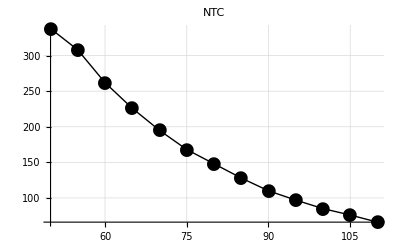

{{50,55,60,65,70,75,80,85,90,95,100,105,110},{338,308,262,226,195,168,148,128,110,97,85,76,66}}

/Users/timfeirg/Documents/Medical-Sensor-Experiments/Exp12_NTC.xlsx

```mathematica
(*Exp12*)
temperature=Range[50,110,5];
resistance={338,308,262,226,195,168,148,128,110,97,85,76,66};
coordinatesExp=Transpose[{temperature,resistance}];
linearFitExp=LinearModelFit[coordinatesExp,x,x];
PlotGraph=ListLinePlot[
coordinatesExp,
PlotMarkers->{Automatic,18},
PlotStyle->{Black,Thick},
GridLines->Automatic,
GridLinesStyle->Directive[Black,Dashed],
Frame->Automatic,
FrameLabel->{"T/°C","R/kΩ"},
PlotLabel->"NTC",
BaseStyle->{FontWeight->"Bold",FontSize->18}
]
fullForm={temperature,resistance}
Export["/Users/timfeirg/Documents/Medical-Sensor-Experiments/Exp12_NTC.xlsx",fullForm,"XLSX"]
```

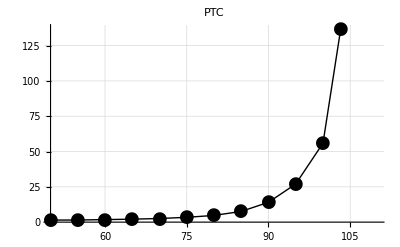

{{50,55,60,65,70,75,80,85,90,95,100,105,110},{1.45,1.5,1.79,2.1,2.57,3.41,4.75,7.59,14.06,27.,55.9,180.1,727}}

/Users/timfeirg/Documents/Medical-Sensor-Experiments/Exp12_PTC.xlsx

```mathematica
temperature=Range[50,110,5];
resistance={1.45,1.50,1.79,2.10,2.57,3.41,4.75,7.59,14.06,27.00,55.90,180.1,727};
coordinatesExp=Transpose[{temperature,resistance}];
linearFitExp=LinearModelFit[coordinatesExp,x,x];
PlotGraph=ListLinePlot[
coordinatesExp,
PlotMarkers->{Automatic,18},
PlotStyle->{Black,Thick},
GridLines->Automatic,
GridLinesStyle->Directive[Black,Dashed],
Frame->Automatic,
FrameLabel->{"T/°C","R/kΩ"},
PlotLabel->"PTC",
BaseStyle->{FontWeight->"Bold",FontSize->18}
]
fullForm={temperature,resistance}
Export["/Users/timfeirg/Documents/Medical-Sensor-Experiments/Exp12_PTC.xlsx",fullForm,"XLSX"]
```